```mathematica
ssefsin=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_sin.dat"];
error=Table[{ssefsin[[i,1]],Log[10,Abs[Sin[ ssefsin[[i,1]]]- ssefsin[[i,2]]]]}, {i,1,ssefsin//Length}];
```

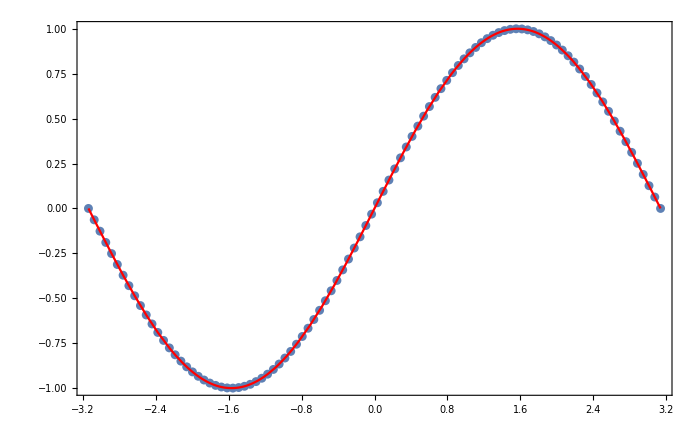

```mathematica
Show[
ListPlot[ssefsin, PlotRange->All, Frame->True, ImageSize->700],
Plot[Sin[x],{x,-Pi,Pi}, PlotStyle->Red]
]
```

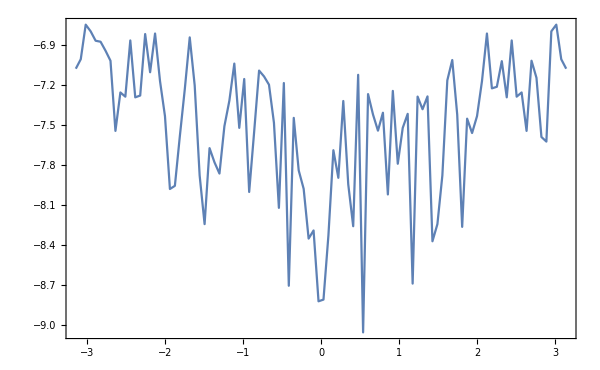

```mathematica
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

```mathematica
ssefcos=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_cos.dat"];
error=Table[{ssefcos[[i,1]],Log[10,Abs[Cos[ ssefcos[[i,1]]]- ssefcos[[i,2]]]]}, {i,1,ssefcos//Length}];
```

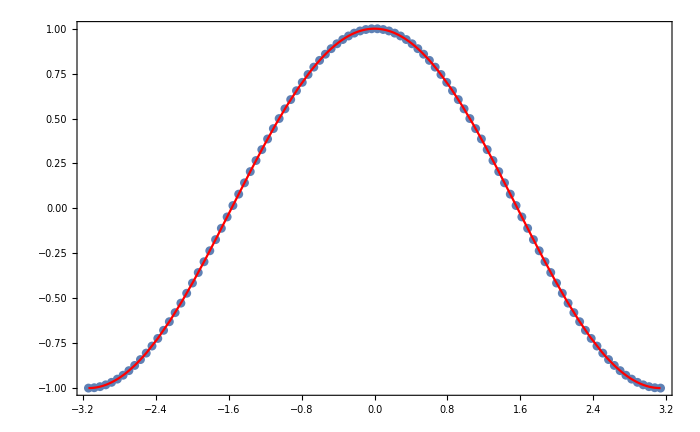

```mathematica
Show[
ListPlot[ssefcos, PlotRange->All, Frame->True, ImageSize->700],
Plot[Cos[x],{x,-Pi,Pi}, PlotStyle->Red]
]
```

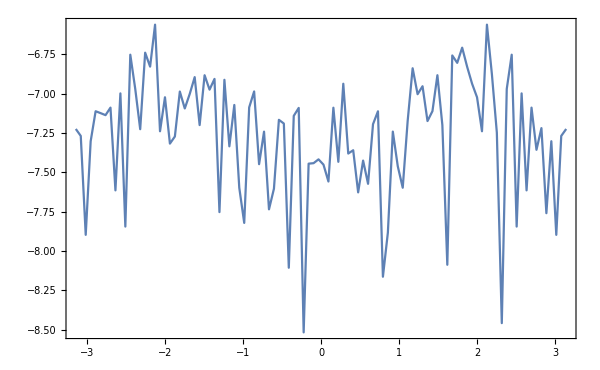

```mathematica
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

```mathematica
sseftan=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_tan.dat"];
error=Table[{sseftan[[i,1]],Log[10,Abs[Tan[ sseftan[[i,1]]]- sseftan[[i,2]]]]}, {i,1,ssefsin//Length}];
```

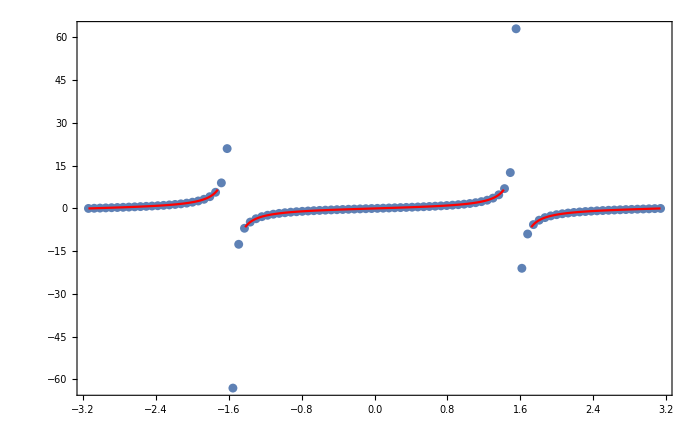

```mathematica
Show[
ListPlot[sseftan, PlotRange->All, Frame->True, ImageSize->700],
Plot[Tan[x],{x,-Pi,Pi}, PlotStyle->Red]
]
```

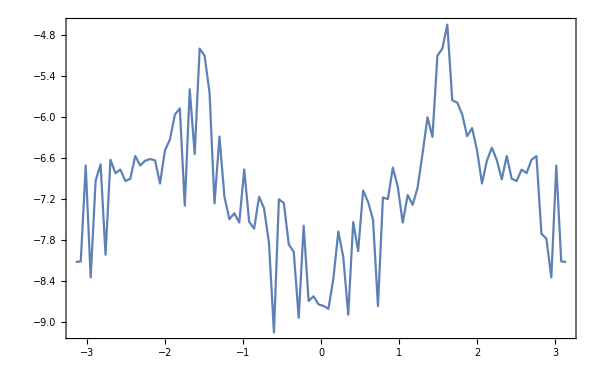

```mathematica
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

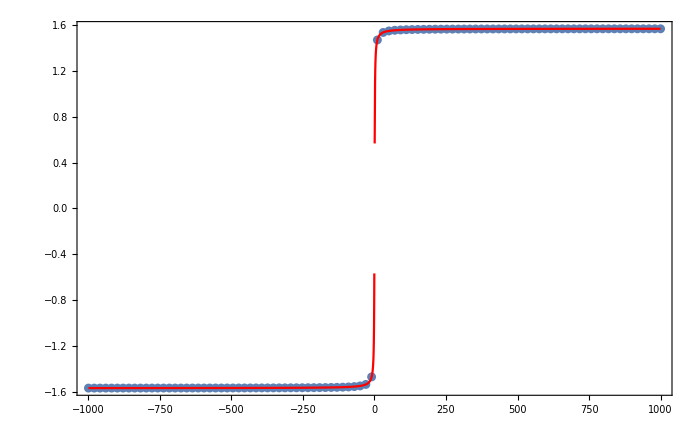

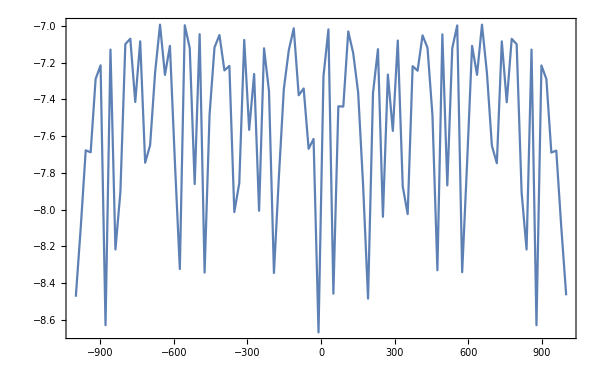

```mathematica
ssefarctan=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_arctan.dat"];
error=Table[{ssefarctan[[i,1]],Log[10,Abs[ArcTan[ ssefarctan[[i,1]]]- ssefarctan[[i,2]]]]}, {i,1,ssefarctan//Length}];
Show[
ListPlot[ssefarctan, PlotRange->All, Frame->True, ImageSize->700],
Plot[ArcTan[x],{x,-1000,1000}, PlotStyle->Red]
]
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

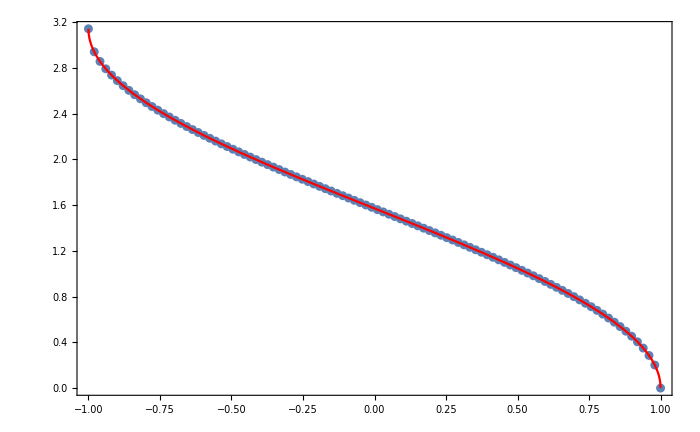

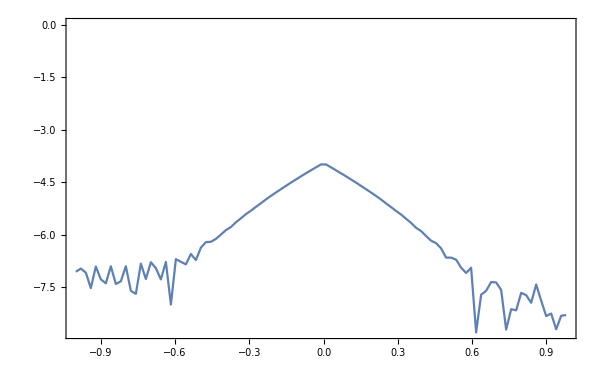

```mathematica
ssefarccos=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_arccos.dat"];
error=Table[{ssefarccos[[i,1]],Log[10,Abs[ArcCos[ ssefarccos[[i,1]]]- ssefarccos[[i,2]]]]}, {i,1,ssefarccos//Length}];
Show[
ListPlot[ssefarccos, PlotRange->All, Frame->True, ImageSize->700],
Plot[ArcCos[x],{x,-1,1}, PlotStyle->Red]
]
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

{{-1,3.1415927410125732},{-0.97979795932769775,2.9402451515197754},{-0.95959597826004028,2.8563592433929443},{-0.93939393758773804,2.7916545867919922},{-0.91919189691543579,2.7368199825286865},{-0.89899,2.6882541179656982},{-0.87878787517547607,2.6441125869750977},{-0.85858583450317383,2.6033},{-0.83838385343551636,2.5651078224182129},{-0.81818181276321411,2.52904},{-0.79797977209091187,2.494732141494751},{-0.7777777910232544,2.4619190692901611},{-0.75757575035095215,2.4303874969482422},{-0.7373737096786499,2.3999705314636231},{-0.71717172861099243,2.3705317974090576},{-0.69696968793869019,2.3419594764709473},{-0.67676770687103272,2.314159631729126},{-0.65656566619873047,2.2870528697967529},{-0.63636362552642822,2.2605714797973633},{-0.61616164445877075,2.2346563339233398},{-0.59595960378646851,2.209256649017334},{-0.575758,2.18433},{-0.55555558204650879,2.159827470779419},{-0.53535354137420654,2.1357228755950928},{-0.5151515007019043,2.1119809150695801},{-0.49494948983192444,2.0885734558105469},{-0.474747,2.0654740333557129},{-0.45454546809196472,2.042658805847168},{-0.43434342741966248,2.020106315612793},{-0.41414141654968262,1.9977966547012329},{-0.39393940567970276,1.9757112264633179},{-0.37373736500740051,1.9538331031799316},{-0.35353535413742065,1.932146430015564},{-0.3333333432674408,1.91064},{-0.313131,1.8892885446548462},{-0.29292929172515869,1.8680902719497681},{-0.27272728085517883,1.8470292091369629},{-0.25252524018287659,1.8260934352874756},{-0.23232322931289673,1.8052719831466675},{-0.212121,1.7845542430877686},{-0.19191919267177582,1.7639297246932983},{-0.17171716690063477,1.7433887720108032},{-0.15151515603065491,1.7229220867156982},{-0.13131313025951386,1.702520489692688},{-0.111111,1.68218},{-0.090909093618392944,1.6618776321411133},{-0.070707067847251892,1.6416193246841431},{-0.050505049526691437,1.6213921308517456},{-0.030303031206130981,1.6011878252029419},{-0.010101011022925377,1.5809991359710693},{0.010101009160280228,1.5605936050415039},{0.030303029343485832,1.5404049158096314},{0.050505049526691437,1.5202006101608276},{0.070707067847251892,1.4999734163284302},{0.090909093618392944,1.47971510887146},{0.111111,1.4594175815582275},{0.13131313025951386,1.4390722513198853},{0.15151515603065491,1.41867},{0.17171716690063477,1.39820396900177},{0.19191919267177582,1.37766},{0.212121,1.3570384979248047},{0.23232322931289673,1.3363207578659058},{0.25252524018287659,1.3154993057250977},{0.27272728085517883,1.2945635318756104},{0.29292929172515869,1.2735024690628052},{0.313131,1.2523041963577271},{0.3333333432674408,1.2309564352035523},{0.35353535413742065,1.2094463109970093},{0.37373736500740051,1.18776},{0.39393940567970276,1.1658815145492554},{0.41414141654968262,1.1437960863113403},{0.43434342741966248,1.1214864253997803},{0.45454543828964233,1.0989339351654053},{0.474747,1.07612},{0.49494948983192444,1.0530194044113159},{0.5151515007019043,1.0296117067337036},{0.53535354137420654,1.0058698654174805},{0.55555558204650879,0.98176521062850952},{0.575758,0.95726585388183594},{0.59595960378646851,0.93233609199523926},{0.61616158485412598,0.90693634748458862},{0.63636362552642822,0.88102132081985474},{0.65656566619873047,0.85453981161117554},{0.67676764726638794,0.82743322849273682},{0.69696968793869019,0.79963338375091553},{0.71717172861099243,0.771061},{0.7373737096786499,0.74162226915359497},{0.75757575035095215,0.71120518445968628},{0.7777777910232544,0.67967373132705689},{0.79797977209091187,0.64686065912246704},{0.81818181276321411,0.61255472898483276},{0.83838385343551636,0.57648491859436035},{0.85858583450317383,0.53829145431518555},{0.87878787517547607,0.49748009443283081},{0.89899,0.45333856344223023},{0.91919189691543579,0.40477278828620911},{0.93939393758773804,0.34993812441825867},{0.95959597826004028,0.28523346781730652},{0.97979795932769775,0.20134758949279785},{1,0}}

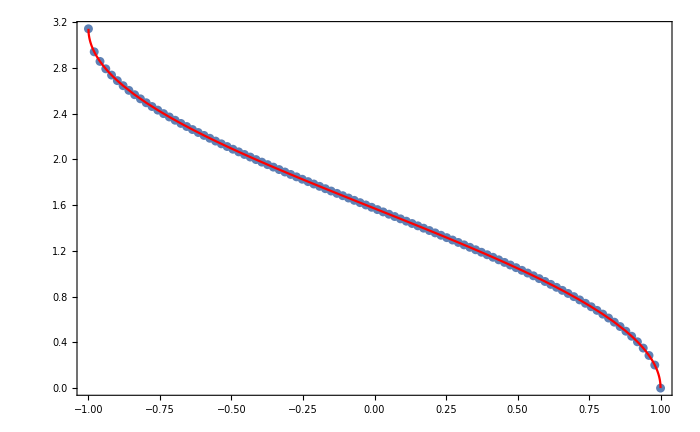

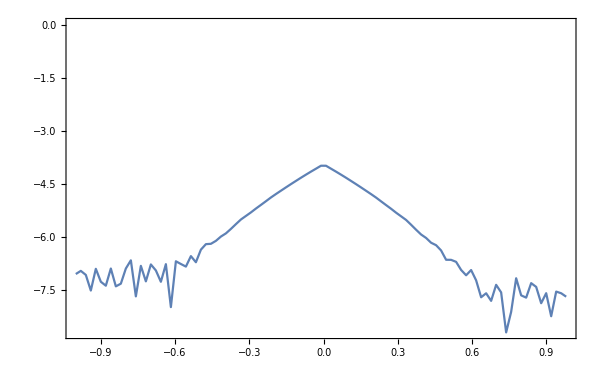

```mathematica
ssefarccos=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_arccos_ver2.dat"]
error=Table[{ssefarccos[[i,1]],Log[10,Abs[ArcCos[ ssefarccos[[i,1]]]- ssefarccos[[i,2]]]]}, {i,1,ssefarccos//Length}];
Show[
ListPlot[ssefarccos, PlotRange->All, Frame->True, ImageSize->700],
Plot[ArcCos[x],{x,-1,1}, PlotStyle->Red]
]
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

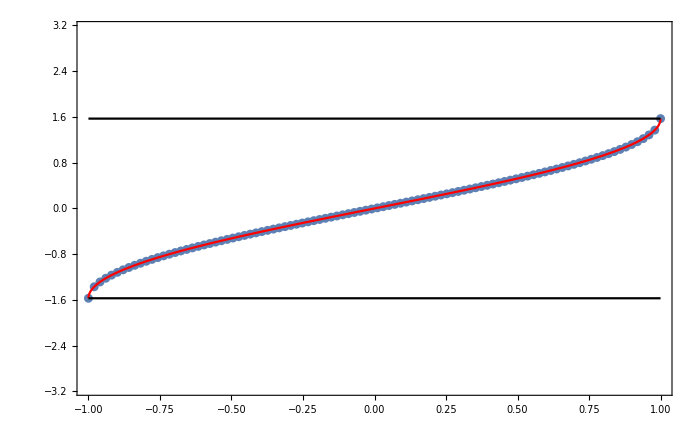

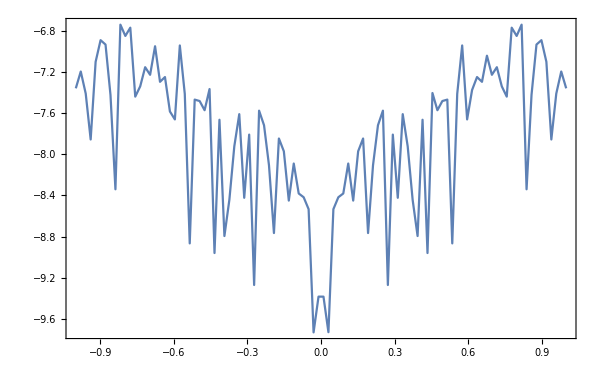

```mathematica
ssefarcsin=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_arcsin.dat"];
error=Table[{ssefarcsin[[i,1]],Log[10,Abs[ArcSin[ ssefarcsin[[i,1]]]- ssefarcsin[[i,2]]]]}, {i,1,ssefarcsin//Length}];
Show[
ListPlot[ssefarcsin, PlotRange->{-Pi, Pi}, Frame->True, ImageSize->700],
Plot[ArcSin[x],{x,-1,1}, PlotStyle->Red],
ParametricPlot[{t, Pi/2},{t,-1,1}, PlotStyle->Black],
ParametricPlot[{t, -Pi/2},{t,-1,1}, PlotStyle->Black]
]
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

```mathematica
0.71^45
```

2.02594×10^-7